```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->"DiANE.m"]
```

# DiANE - Diagram Arts and Notation of Equations

## Exports

```mathematica
FPrint::usage=""
FPrint[expr_]/;Head[$GlobalSetup]=!=Symbol:=FPrint[$GlobalSetup,expr];

FTex::usage=""
FTex[expr_]/;Head[$GlobalSetup]=!=Symbol:=FTex[$GlobalSetup,expr];
```

## Global variables

```mathematica
ModuleLoaded::dependency="The module `1` requires `2`, which has not been loaded.";

If[ModuleLoaded[FunKit]=!=True,
Message[ModuleLoaded::dependency,"DiANE","FunKit"];
Abort[];
];

If[ModuleLoaded[FEDeriK]=!=True,
Message[ModuleLoaded::dependency,"DiANE","FEDeriK"];
Abort[];
];

ModuleLoaded[DiANE]=True;
```

```mathematica
$FunKitDirectory=SelectFirst[Join[{FileNameJoin[{$UserBaseDirectory,"Applications","FunKit"}],FileNameJoin[{$BaseDirectory,"Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Packages","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","ExtraPackages","FunKit"}]},Select[$Path,StringContainsQ[#,"FunKit"]&]],DirectoryQ[#]&]<>"/";
```

## Pretty printing and LaTeX

### Load packages

```mathematica
If[Length@PacletFind["MaTeX"]===0,
ResourceFunction["MaTeXInstall"][]
]
Get["MaTeX`"]
Import[$FunKitDirectory<>"/utils/MathematicaTeXUtilities.m"]
```

### Index list formatting

```mathematica
MakeTexIndexList[{i__}]:=Module[
{
ni=Length[{i}],
isLower,
indices={i},
lowerList,
upperList,
removeTrailingPhantoms
},

isLower=Map[MatchQ[#,Times[-1,_]]&,{i}];
indices=Table[If[isLower[[idx]],-indices[[idx]],indices[[idx]]],{idx,1,ni}];

lowerList=Table[
If[isLower[[idx]],
ToString@TeXForm[indices[[idx]]],
"\\phantom{"<>ToString@TeXForm[indices[[idx]]]<>"}"
],
{idx,1,ni}];

upperList=Table[
If[isLower[[idx]],
"\\phantom{"<>ToString@TeXForm[indices[[idx]]]<>"}",
ToString@TeXForm[indices[[idx]]]
],
{idx,1,ni}];

removeTrailingPhantoms[l_]:=Module[{ret=l},
While[StringContainsQ[ret[[-1]],"\\phantom"],
ret=Delete[ret,-1];
If[Length[ret]===0,Return[{""}]];
];
Return[ret];
];

upperList=removeTrailingPhantoms@upperList;
lowerList=removeTrailingPhantoms@lowerList;

Return[{StringJoin@@lowerList,StringJoin@@upperList}]
]
```

```mathematica
MakeIdxField[f_,i_,up]:=MakeIdxField[f,If[MatchQ[i,Times[-1,_]],-i,i]]
MakeIdxField[f_,i_,down]:=MakeIdxField[f,If[MatchQ[i,Times[-1,_]],i,-i]]
MakeIdxField[f_,i_]:=Module[{isLower,idx},
isLower=MatchQ[i,Times[-1,_]];
idx=If[isLower,-i,i];
If[f===AnyField,Return[ToString[TeXForm[idx]]]];
If[isLower,Return[ToString@TeXForm[Subscript[f,idx]]]];
Return[ToString@TeXForm[Superscript[f,idx]]]
]

MakeTexIndexList[{f__},{i__}]:=Module[
{
ni=Length[{f}],
isLower,
fields={f},
indices={i},
lowerList,
upperList,
removeTrailingPhantoms
},

isLower=Map[MatchQ[#,Times[-1,_]]&,{i}];

lowerList=Table[
If[isLower[[idx]],
MakeIdxField[fields[[idx]],indices[[idx]],up],
"\\phantom{"<>MakeIdxField[fields[[idx]],indices[[idx]],up]<>"}"
],
{idx,1,ni}];

upperList=Table[
If[isLower[[idx]],
"\\phantom{"<>MakeIdxField[fields[[idx]],indices[[idx]],up]<>"}",
MakeIdxField[fields[[idx]],indices[[idx]],up]
],
{idx,1,ni}];

removeTrailingPhantoms[l_]:=Module[{ret=l},
While[StringContainsQ[ret[[-1]],"\\phantom"],
ret=Delete[ret,-1];
If[Length[ret]===0,Return[{""}]];
];
Return[ret];
];

upperList=removeTrailingPhantoms@upperList;
lowerList=removeTrailingPhantoms@lowerList;

Return[{StringJoin@@lowerList,StringJoin@@upperList}]
]
```

### Prettify closed indices

```mathematica
prettySuperIndices[setup_,expr_FEq]:=Map[prettySuperIndices[setup,#]&,expr];
prettySuperIndices[setup_,expr_FTerm]:=Module[{closedIndices,openIndices,repl,indices},
closedIndices=GetClosedSuperIndices[setup,expr];
openIndices=GetOpenSuperIndices[setup,expr];
indices=Alphabet[];
Do[
indices=Select[indices,#=!=ToString[openIndices[[i]]]&],
{i,1,Length[openIndices]}
];
repl=Thread[closedIndices->indices[[1;;Length[closedIndices]]]];
Return[expr//.repl]
];
prettySuperIndices[setup_,expr_]:=expr/.FEq[a___]:>prettySuperIndices[setup,FEq[a]]
```

```mathematica
prettyExplicitIndices[setup_,expr_FEq]:=Map[prettyExplicitIndices[setup,#]&,expr];
prettyExplicitIndices[setup_,expr_FTerm]:=Module[{allIndices,closedIndices,openIndices,repl,indices},
allIndices=Select[ExtractObjectsAndIndices[setup,expr][[2]],Head[#]===List&];
allIndices=allIndices[[All,2]];
closedIndices=Pick[allIndices,Count[allIndices,#]===2&/@allIndices];
openIndices=Pick[allIndices,Count[allIndices,#]=!=2&/@allIndices];
indices=Alphabet[];
repl=Thread[closedIndices->indices[[1;;Length[closedIndices]]]]∪Thread[openIndices->indices[[Length[closedIndices]+1;;Length[closedIndices]+Length[openIndices]]]];
Return[expr//.repl]
];
prettyExplicitIndices[setup_,expr_]:=expr/.FEq[a___]:>prettyExplicitIndices[setup,FEq[a]]
```

### General formatting definitions

```mathematica
$TexStyles={};
$Fields={};
```

```mathematica
AddTexStyles::invalidRule="The given set of style rules does not follow the pattern Symbol->String.";

AddTexStyles[a__Rule]:=Module[{},
If[Or@@Map[Head[#]=!=String&,Values[{a}]],
Message[AddTexStyles::invalidRule];Abort[]];
$TexStyles=DeleteDuplicates[Join[$TexStyles,{a}]];
]

SetTexStyles[a__Rule]:=Module[{},
If[Or@@Map[Head[#]=!=String&,Values[{a}]],
Message[AddTexStyles::invalidRule];Abort[]];
$TexStyles=DeleteDuplicates[{a}];
]

SetTexStyles[]:=Module[{},
$TexStyles={};
]
```

```mathematica
isRoutedAssociation[expr_]:=Module[{},
If[Head[expr]=!=Association,Return[False]];
If[FreeQ[Keys[expr],"result"],Return[False]];
If[FreeQ[Keys[expr],"externalIndices"],Return[False]];
If[FreeQ[Keys[expr],"loopMomenta"],Return[False]];
Return[True];
]
Protect[routedContainer];
```

```mathematica
RenewFormatDefinitions[]:=Module[{},

Unprotect[FDOp,GammaN,Propagator,Rdot,FTerm,FEq,γ,δ,FMinus,S,routedContainer];
Unprotect@@$allObjects;

(*Field formatting with superindices*)
Map[
(
Format[Keys[#][any_],TeXForm]:=Module[{head,arg},
head=Keys[#]//.$TexStyles//.$Fields;
arg=Format[any,TeXForm]//ToString;
TeXVerbatim[head<>arg]
];
Format[Superscript[Keys[#],any_],TeXForm]:=Module[{head,arg},
head=Keys[#]//.$TexStyles//.$Fields;
arg=Format[any,TeXForm]//ToString;
TeXVerbatim[head<>"^"<>arg]
];
Format[Subscript[Keys[#],any_],TeXForm]:=Module[{head,arg},
head=Keys[#]//.$TexStyles//.$Fields;
arg=Format[any,TeXForm]//ToString;
TeXVerbatim[head<>"_"<>arg]
];
)&,
$TexStyles∪Select[$Fields,FreeQ[Keys[$TexStyles],Keys[#]]&]];

(*Field formatting with explicit indices*)
Map[
(
Format[Keys[#][{p_,indices_}],TeXForm]:=Module[{head,arg},
head=Keys[#]//.$TexStyles//.$Fields;
arg=Format[indices,TeXForm]//ToString;
TeXVerbatim[head<>arg<>"("<>ToString[TeXForm[p]]<>")"]
];
Format[Superscript[Keys[#],{p_,indices_}],TeXForm]:=Module[{head,arg},
head=Keys[#]//.$TexStyles//.$Fields;
arg=Format[indices,TeXForm]//ToString;
TeXVerbatim[head<>"^"<>arg<>"("<>ToString[TeXForm[p]]<>")"]
];
Format[Subscript[Keys[#],{p_,indices_}],TeXForm]:=Module[{head,arg},
head=Keys[#]//.$TexStyles//.$Fields;
arg=Format[indices,TeXForm]//ToString;
TeXVerbatim[head<>"_"<>arg<>"("<>ToString[TeXForm[p]]<>")"]
];
)&,
$TexStyles∪Select[$Fields,FreeQ[Keys[$TexStyles],Keys[#]]&]];

(*Other formatting*)
Format[FDOp[f_],TeXForm]:=Module[{},
TeXDelimited["\\frac{\\delta}{\\delta",f,"}"]
];

Map[
(Format[#[{f__},{i__}],TeXForm]/;Head[{i}[[1]]]=!=List:=Module[{sub,sup,ret},
{sub,sup}=MakeTexIndexList[{f},{i}];
ret=Switch[#,
Propagator,"G",
FMinus,"(-1)",
Rdot,"\\partial_t R",
GammaN,"\\Gamma",
S,"S",
_,TeXForm[#]//ToString
];
If[StringLength[sub]=!=0,ret=ret<>"_{"<>sub<>"}"];
If[StringLength[sup]=!=0,ret=ret<>"^{"<>sup<>"}"];
TeXVerbatim[ret]
])&,
$indexedObjects];

Map[
(Format[#[{f__},{i__}],TeXForm]/;Head[{i}[[1]]]===List:=Module[{sub,sup,ret},
{sub,sup}=MakeTexIndexList[{f},-{i}[[All,2]]];
ret=Switch[#,
Propagator,"G",
FMinus,"(-1)",
Rdot,"\\partial_t R",
GammaN,"\\Gamma",
S,"S",
_,TeXForm[#]//ToString
];
If[StringLength[sub]=!=0,ret=ret<>"_{"<>sub<>"}"];
If[StringLength[sup]=!=0,ret=ret<>"^{"<>sup<>"}"];
TeXVerbatim[ret<>"("<>StringRiffle[Map[ToString@TeXForm[#]&,{i}[[All,1]]],","]<>")"]
])&,
$indexedObjects];

Format[FTerm[a___],TeXForm]:=Module[{obj,integrals,replNames,idx,prefix,postfix,body={a}},
integrals=Pick[$availableLoopMomenta,Map[MemberQ[{a},#,Infinity]&,$availableLoopMomenta]];
replNames=Thread[$availableLoopMomenta->Table[Subscript[Symbol[$loopMomentumName],idx],{idx,1,Length[$availableLoopMomenta]}]];
prefix=StringJoin[Map["\\int_{"<>ToString[TeXForm[#]]<>"}"&,integrals//.replNames]];
postfix="";

If[MatchQ[{a}[[1]],b_/;NumericQ[b]&&b<0],
If[{a}[[1]]===-1,
prefix=prefix<>"(-";
postfix=")"<>postfix;
body=body[[2;;]];
,
prefix=prefix<>"(";
postfix=")"<>postfix;
]
];

body=body//.replNames;
body=body//.Map[#->Subscript[Symbol[StringTake[SymbolName[#],{1}]],ToExpression@StringTake[SymbolName[#],{2,-1}]]&,
Select[GetAllSymbols[body],StringMatchQ[SymbolName[#],LetterCharacter~~DigitCharacter..]&]
];

TeXDelimited[prefix,##,postfix,
"DelimSeparator"->"","BodySeparator"->"\\,",
(*It is not clear why the call to RenewFormatDefinitions[] is necessary here. However, removing it leads to TeXForm ignoring all custom TeXStyles.*)
"BodyConverter"->(ToString[RenewFormatDefinitions[];Format[#,TeXForm]]&)
]&@@body
];

Format[FEq[a___],TeXForm]:=If[Length[Flatten[(List@@#&)/@{a}]]<=10,
TeXDelimited["",a,"",
"DelimSeparator"->"\n","BodySeparator"->"\n\\,+\\,\n",
"BodyConverter"->(ToString[Format[#,TeXForm]]&)],
TeXDelimited["\\begin{aligned}&",a,"\\end{aligned}",
"DelimSeparator"->"\n","BodySeparator"->"\n\\\\ &\\,+\\,\n",
"BodyConverter"->(ToString[Format[#,TeXForm]]&)]
];

Format[routedContainer[a__],TeXForm]/;(And@@(isRoutedAssociation/@{a})):=Module[{parts},
parts={a}[[All,Key["result"]]];
parts=ToString[TeXForm[FEq[#]]]&/@parts;

parts=Join[
{parts[[1]]},
Map[
If[StringTake[#,{1,17}]==="\\begin{aligned}&\n",
StringJoin[{"\\begin{aligned}&\n\\,+\\,",StringTake[#,{18,-1}]}],
StringJoin[{"\\,+\\,",#}]]&,
parts[[2;;]]]
];

TeXVerbatim["\\begin{aligned}&\n"<>
StringRiffle[parts,"\n \\\&\n"]<>
"\n\\end{aligned}"]
];


Protect[FDOp,GammaN,Propagator,Rdot,FTerm,FEq,γ,δ,FMinus,S,routedContainer];
Protect@@$allObjects;
];

TakeDerivatives[MakeDSE[c[x]],{A[z],cb[y]}]//.{A[_]:>0,c[_]:>0,cb[_]:>0}//Truncate;
RouteIndices[Setup,%];
%//FPrint
```

-Graphics-

### FPrint and FTex commands

```mathematica
(*Turn a given expression into LaTeX code*)
FTex[setup_,expr_]:=Module[
{prExp=expr,fields},
AssertFSetup[setup];
fields=GetAllFields[setup];

(*update the formatting definitions for TeXForm*)
$Fields=Thread[fields->Map[ToString[TeXForm[#]]&,fields]];
RenewFormatDefinitions[];

(*Assign human-readable superindices*)
prExp=prettySuperIndices[setup,prExp];
prExp=prettyExplicitIndices[setup,prExp];

(*make fields with indices to sub-/super-script*)
prExp=prExp//.Map[#[Times[-1,a_]]:>Subscript[#,a]&,fields]//.Map[#[a_]:>Superscript[#,a]&,fields];

(*For correct rendering, fully expand any FTerms*)
prExp=prExp//.FTerm[pre___,Times[a_,b_],post___]:>FTerm[pre,a,b,post];

Return[prExp//TeXForm];
];

(*For the output of a full routing*)
FTex[setup_,expr_List]/;(And@@(isRoutedAssociation/@expr)):=FTex[setup,routedContainer@@expr];

(*For direct printing*)
FPrint[setup_,expr_]:=Print[FTex[setup,expr]//MaTeX];
```

## Diagram drawing

```mathematica
GetEdgeRule[setup_,vertices_,fields_]:=Module[{fermions,bosons,sel},
If[Length[obj]!=Length[fields]||Length[obj]!=2,Print["Mismatch!"];Abort[]];
fermions=GetFermionPairs[setup];
bosons=GetBosons[setup];

If[MemberQ[fermions,fields[[1]],Infinity]&&MemberQ[fermions,fields[[2]],Infinity],
sel=Select[fermions,MemberQ[#,fields[[1]],Infinity]&][[1]];
If[fields===sel,
Return[obj[[1]]->obj[[2]]],
Return[obj[[2]]->obj[[1]]];
]
];

If[MemberQ[bosons,fields[[1]],Infinity]&&MemberQ[bosons,fields[[2]],Infinity],
Return[obj[[1]]<->obj[[2]]]
];

Print["fields ",fields," not found!"];
Abort[];
];
```

```mathematica
MakeEdgeStyle[style_,setup_]:=Module[{corStyle,havePairs,allPairs,missingPairs},
corStyle=style/.{
a_[c_,d_]/;
a===Rule&&Head[c]=!=List:>
Sort[{c,GetPartnerField[c,setup]}]->d};
corStyle=corStyle/.{a_[{c__},d_]/;a===Rule:>Sort[{c}]->d};

havePairs=corStyle/.{a_[{c__},d_]/;a===Rule:>{c}};
allPairs=Join[Map[{#,#}&,GetBosons[setup]],Map[Sort,GetFermionPairs[setup]]];
missingPairs=DeleteCases[allPairs,Alternatives@@havePairs];
corStyle=Join[corStyle,Thread[missingPairs->ColorData[97,"ColorList"][[1;;Length[missingPairs]]]]];
Return[corStyle]
];
```

```mathematica
arcFunc[g_,r_:1.5][list_,DirectedEdge[x_,x_]]:=With[{v=DynamicLocation["VertexID$"<>ToString[VertexIndex[g,x]],Automatic,Center]},Arrow[BezierCurve[Join[{v},ScalingTransform[r {1,1},list[[1]]][list[[{5,8,10,16,18,21}]]],{v}],SplineDegree->7]]]
arcFuncUn[g_,r_:1.5][list_,UndirectedEdge[x_,x_]]:=With[{v=DynamicLocation["VertexID$"<>ToString[VertexIndex[g,x]],Automatic,Center]},Arrow[BezierCurve[Join[{v},ScalingTransform[r {1,1},list[[1]]][list[[{5,8,10,16,18,21}]]],{v}],SplineDegree->7]]]
```

```mathematica
PlotOneSuperindexDiagram[diag_,setup_,OptionsPattern[]]:=Module[
{ShowEdgeLabels,EdgeStyle,
transformedDiag,vertices,edges,prefactor,
externalLegs,externalIndices,idx,field,partnerField,outerIdx,externalLeg,
regulatorVertex,curVertex,rules,corStyle,cross,
explVertices,explEdges,vertexShapes,vertexLabels,edgeLabels,
graph},

AssertIsSuperindexDiagram[diag];

EdgeStyle=OptionValue["EdgeStyle"];
ShowEdgeLabels=OptionValue["ShowEdgeLabels"];

transformedDiag=Map[
If[Head[#]===Association,
If[#["type"]=="Propagator",
<|
"Rule"->GetEdgeRule[{#["indices"][[1,2]],#["indices"][[2,2]]},{#["indices"][[1,1]],#["indices"][[2,1]]},setup],
"Style"->Sort[{#["indices"][[1,1]],#["indices"][[2,1]]}]
|>,
<|
"Vertex"->#["indices"][[All,2]],
"Style"->#["type"]
|>],
#]&
,diag];

vertices=Select[transformedDiag,MemberQ[Keys[#],"Vertex",Infinity]&];
edges=Select[transformedDiag,MemberQ[Keys[#],"Rule",Infinity]&];
prefactor=("Prefactor"/.transformedDiag[[1]])[[1]];

externalLegs=GetExternalIndices[diag];
externalIndices={};
For[idx=1,idx<=Length[externalLegs],idx++,
field=externalLegs[[idx,1]];
partnerField=GetPartnerField[field,setup];
outerIdx=Unique[externalLeg];
externalIndices=Join[externalIndices,{outerIdx}];
vertices=vertices∪{<|
"Vertex"->{{outerIdx}},
"Style"->externalLeg[field]
|>};
edges=edges∪{<|
"Rule"->GetEdgeRule[{externalLegs[[idx,2]],{outerIdx}},{field,partnerField},setup],"Style"->Sort[{field,partnerField}]
|>};
];

regulatorVertex=0;
For[idx=1,idx<=Length[vertices],idx++,
curVertex=vertices[[idx]]["Vertex"];
If[Length[curVertex]>1,
rules=Map[#->curVertex[[1]]&,curVertex[[2;;]]];
vertices=vertices/.rules;
edges=edges/.rules;
];
vertices[[idx]]=<|"Vertex"->vertices[[idx]]["Vertex"][[1]],"Style"->vertices[[idx]]["Style"]|>;
If[vertices[[idx]]["Style"]=="Regulatordot",regulatorVertex=vertices[[idx]]["Vertex"]];
];

corStyle=MakeEdgeStyle[EdgeStyle,setup];

 cross[r_] := Graphics[{Thick, Line[{{r / Sqrt[2], r / Sqrt[2]
            }, {-r / Sqrt[2], -r / Sqrt[2]}}], Line[{{r / Sqrt[2], -r / Sqrt[2]},
             {-r / Sqrt[2], r / Sqrt[2]}}], Circle[{0, 0}, r]}];

explVertices=Map[#["Vertex"]&,vertices];
vertexShapes=Join[
{regulatorVertex->cross[1]}
];
vertexLabels=Map[
#["Vertex"]->(#["Style"]/.a_[b_]:>b)&
,
Select[vertices,Head[#["Style"]]===externalLeg&]
];
explEdges=Map[Style[#["Rule"],#["Style"]/.corStyle]&,edges];
edgeLabels=If[ShowEdgeLabels,
Map[#["Rule"]->ToString[#["Style"][[1]]]<>ToString[#["Style"][[2]]]&,edges],
{}
];

Return[
{prefactor,
graph=Graph[explVertices,explEdges];
Graph[graph,
VertexShape->vertexShapes,
VertexLabels->vertexLabels,
VertexSize -> {regulatorVertex -> Medium},
EdgeLabels->edgeLabels,
EdgeShapeFunction->{x_->x_:>arcFunc[graph,20.0],x_<->x_:>arcFuncUn[graph,20.0]},
PerformanceGoal->"Quality"
]
}
];
];
Options[PlotOneSuperindexDiagram]={"ShowEdgeLabels"->False,"EdgeStyle"->{}};

PlotSuperindexDiagram[diags_List,setup_,a___]:=Module[{},
If[AllTrue[diags,TestIsSuperindexDiagram],
Return[Map[PlotOneSuperindexDiagram[#,setup,a]&,diags]];
];
If[TestIsSuperindexDiagram[diags],
Return[PlotOneSuperindexDiagram[diags,setup,a]];
];
Print["PlotSuperindexDiagram: diagram argument is not a superindex diagram or a list thereof!"];
Abort[];
];
```

# Testing

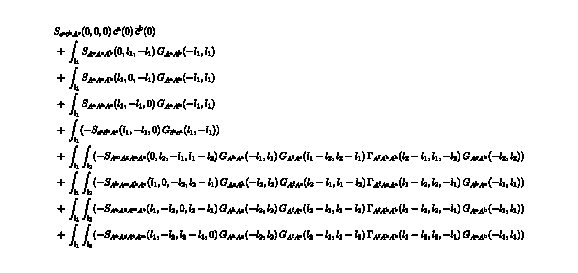

```mathematica
(MakeDSE[A[x]]//.A[_]:>0)//Truncate;
RouteIndices[Setup,%];
%//FPrint
```

Loading modules...

...TensorBases loaded

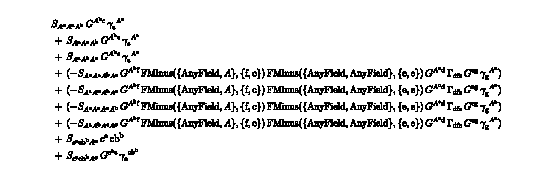

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FunKitInfo[].

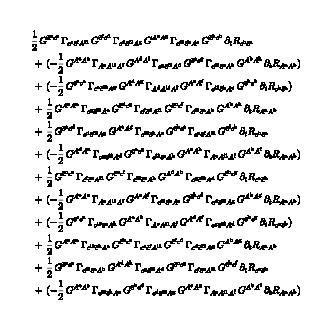

```mathematica
Get["FunKit`"];
fields= <|
"cField"-> {
A[p,{v, c}]
},
"Grassmann"->{
{cb[p,{c}],c[p,{c}]}
}
|>;
truncation=<|
GammaN->{
{A,A},{A,A,A},{A,A,A,A},
{A,cb,c}
},
Propagator->{
{A,A},{cb,c}
},
Rdot->{
{A,A},{cb,c}
},
S->{
{A,A},{A,A,A},{A,A,A,A},
{cb,c},{cb,c,A}
}
|>;
SetTexStyles[cb->"\\bar{c}"];
masterEquation={
{1/2 A[x]VBasis[{A,A},{-x,-y}]A[y]},
{-cb[x]VBasis[{cb,c},{-x,-y}],c[y]}
};
Setup:=<|
"MasterEquation"->masterEquation,
"FieldSpace"->fields,
"Truncation"->truncation
|>;
SetGlobalSetup[Setup];
DerivativeListAcbc={ A[i1],cb[i2],c[i3]};
TakeDerivatives[Setup,WetterichEquation,DerivativeListAcbc];
%//Truncate//FPrint
```